```mathematica
Clear["Global`*"]
```

```mathematica
FourierTransform[t^2,t,ω]
```

-√(2 π) DiracDelta''[ω]

```mathematica
Integrate[Exp[I ω t] t^2,{t,-∞,∞}]
```

Integrate::idiv: Integral of ⅇ^(ⅈ t ω) t^2 does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(ⅈ t ω) t^2ⅆt

```mathematica
Integrate[Exp[I ω t]*1/t,{t,1,∞}]
```

$Aborted

```mathematica
FourierTransform[1/t HeavisideTheta[t],t,ω]
```

(-EulerGamma-Log[Abs[ω]]+1/2 ⅈ π Sign[ω])/(√(2 π))

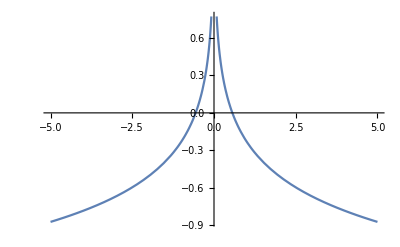

```mathematica
Plot[Re@((-EulerGamma-Log[Abs[ω]]+1/2 ⅈ π Sign[ω])/(√(2 π))),{ω,-5,5}]
```

```mathematica
Integrate[Exp[I ω t]*1/t,{t,1,∞},Assumptions->{ω∈Reals}]
```

Gamma[0,-ⅈ ω]

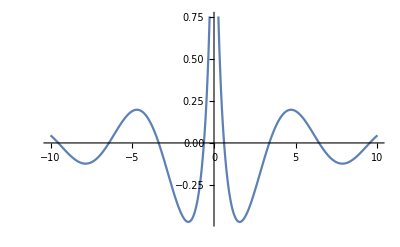

```mathematica
Plot[Re@Gamma[0,-ⅈ ω],{ω,-10,10}]
```

```mathematica
Integrate[Exp[I ω t]*1/t^2,{t,1,∞},Assumptions->{ω∈Reals}]
```

ⅇ^(ⅈ ω)+ⅈ ω Gamma[0,-ⅈ ω]

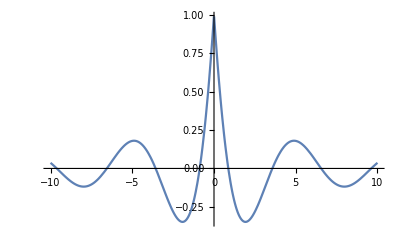

```mathematica
Plot[Re@(ⅇ^(ⅈ ω)+ⅈ ω Gamma[0,-ⅈ ω]),{ω,-10,10}]
```

```mathematica
Integrate[Exp[I ω t]*1/t^1.5,{t,1,∞},Assumptions->{ω∈Reals}]
```

2. HypergeometricPFQ[{-0.25},{0.5,0.75},-ω^2/4]+Abs[ω]^0.5 (-2.50663+(0.+2.50663 ⅈ) Sign[ω])-(0.+2. ⅈ) Abs[ω]^1. HypergeometricPFQ[{0.25},{1.5,1.25},-ω^2/4] Sign[ω]

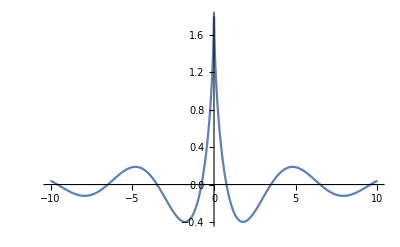

```mathematica
Plot[Re@(1.9999999999999998 HypergeometricPFQ[{-0.25},{0.5,0.75},-ω^2/4]+Abs[ω]^0.5 (-2.5066282746310007+(0.+2.5066282746310007 ⅈ) Sign[ω])-(0.+2.0000000000000004 ⅈ) Abs[ω]^1. HypergeometricPFQ[{0.25},{1.5,1.25},-ω^2/4] Sign[ω]),{ω,-10,10},PlotRange->All]
```

```mathematica
I^(1/I)//N
```

4.81048+0. ⅈ

```mathematica
Exp[π/2.]
```

4.81048